```mathematica
Get["path-integrals-simulations.m"];
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
```

```mathematica
haywardScenario1  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[1]],{j,1,5}]);
```

```mathematica
haywardScenario2  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[2]],{j,1,5}]);
haywardScenario3  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[3]],{j,1,5}]);
haywardScenario4  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[4]],{j,1,5}]);
```

```mathematica
start = 0.1;
time = 0.05;
jumpSize = 1;
selectedNe = 500;
fitVar = 1;
```

```mathematica
(* Scenario 1*)
selCoef = 0.005;
genVar = 0.002249954;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

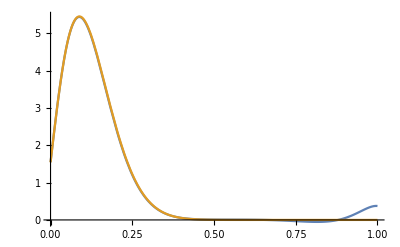

```mathematica
Plot[{Evaluate[haywardScenario1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.880844}. NIntegrate obtained 0.0371009 and 5.75914×10^-8 for the integral and error estimates.

{{0.0185505}}

```mathematica
Export["SimComparison_Scenario1_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario1_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 1.54718

0.01 xxxx 2.29095

0.02 xxxx 3.0052

0.03 xxxx 3.65702

0.04 xxxx 4.2222

0.05 xxxx 4.68488

0.06 xxxx 5.03672

0.07 xxxx 5.27585

0.08 xxxx 5.40574

0.09 xxxx 5.43396

0.1 xxxx 5.37104

0.11 xxxx 5.22939

0.12 xxxx 5.02241

0.13 xxxx 4.76369

0.14 xxxx 4.46642

0.15 xxxx 4.14291

0.16 xxxx 3.80429

0.17 xxxx 3.46027

0.18 xxxx 3.11907

0.19 xxxx 2.78741

0.2 xxxx 2.47054

0.21 xxxx 2.17237

0.22 xxxx 1.89559

0.23 xxxx 1.64182

0.24 xxxx 1.41178

0.25 xxxx 1.20545

0.26 xxxx 1.02221

0.27 xxxx 0.861003

0.28 xxxx 0.720447

0.29 xxxx 0.598947

0.3 xxxx 0.494791

0.31 xxxx 0.406221

0.32 xxxx 0.331499

0.33 xxxx 0.268945

0.34 xxxx 0.216977

0.35 xxxx 0.174132

0.36 xxxx 0.139074

0.37 xxxx 0.110607

0.38 xxxx 0.0876679

0.39 xxxx 0.0693291

0.4 xxxx 0.0547863

0.41 xxxx 0.0433507

0.42 xxxx 0.0344385

0.43 xxxx 0.0275593

0.44 xxxx 0.0223048

0.45 xxxx 0.0183383

0.46 xxxx 0.0153842

0.47 xxxx 0.0132187

0.48 xxxx 0.0116609

0.49 xxxx 0.0105659

0.5 xxxx 0.00981742

0.51 xxxx 0.00932249

0.52 xxxx 0.00900629

0.53 xxxx 0.00880806

0.54 xxxx 0.00867757

0.55 xxxx 0.00857226

0.56 xxxx 0.00845491

0.57 xxxx 0.00829178

0.58 xxxx 0.00805123

0.59 xxxx 0.00770265

0.6 xxxx 0.00721581

0.61 xxxx 0.00656046

0.62 xxxx 0.00570636

0.63 xxxx 0.00462343

0.64 xxxx 0.00328235

0.65 xxxx 0.00165533

0.66 xxxx -0.000282783

0.67 xxxx -0.00255311

0.68 xxxx -0.00517105

0.69 xxxx -0.00814438

0.7 xxxx -0.0114709

0.71 xxxx -0.0151361

0.72 xxxx -0.0191101

0.73 xxxx -0.023345

0.74 xxxx -0.0277715

0.75 xxxx -0.0322961

0.76 xxxx -0.0367971

0.77 xxxx -0.0411225

0.78 xxxx -0.0450863

0.79 xxxx -0.0484671

0.8 xxxx -0.0510059

0.81 xxxx -0.0524062

0.82 xxxx -0.0523344

0.83 xxxx -0.0504236

0.84 xxxx -0.0462781

0.85 xxxx -0.0394828

0.86 xxxx -0.0296151

0.87 xxxx -0.0162626

0.88 xxxx 0.000953721

0.89 xxxx 0.0223488

0.9 xxxx 0.0481342

0.91 xxxx 0.0783681

0.92 xxxx 0.112893

0.93 xxxx 0.151258

0.94 xxxx 0.192625

0.95 xxxx 0.235652

0.96 xxxx 0.278352

0.97 xxxx 0.317925

0.98 xxxx 0.350561

0.99 xxxx 0.37119

1. xxxx 0.373206

```mathematica
(* Scenario 2*)
Clear[selCoef, genVar, blah, statDist];
selCoef = 0.01;
genVar = 0.007050979;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

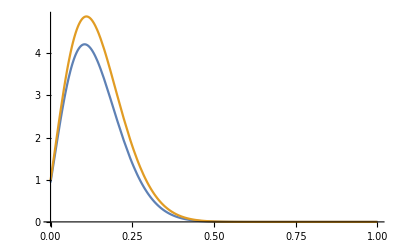

```mathematica
Plot[{Evaluate[haywardScenario2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

{{0.0790496}}

```mathematica
Export["SimComparison_Scenario2_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario2_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 0.935797

0.01 xxxx 1.42266

0.02 xxxx 1.91545

0.03 xxxx 2.39209

0.04 xxxx 2.83406

0.05 xxxx 3.22677

0.06 xxxx 3.55964

0.07 xxxx 3.82588

0.08 xxxx 4.02227

0.09 xxxx 4.14865

0.1 xxxx 4.20748

0.11 xxxx 4.20329

0.12 xxxx 4.14216

0.13 xxxx 4.03123

0.14 xxxx 3.87826

0.15 xxxx 3.69123

0.16 xxxx 3.47803

0.17 xxxx 3.24616

0.18 xxxx 3.00258

0.19 xxxx 2.7535

0.2 xxxx 2.50439

0.21 xxxx 2.25984

0.22 xxxx 2.02363

0.23 xxxx 1.79872

0.24 xxxx 1.58732

0.25 xxxx 1.39093

0.26 xxxx 1.21048

0.27 xxxx 1.04633

0.28 xxxx 0.898457

0.29 xxxx 0.766437

0.3 xxxx 0.649592

0.31 xxxx 0.547037

0.32 xxxx 0.457747

0.33 xxxx 0.380612

0.34 xxxx 0.314484

0.35 xxxx 0.258213

0.36 xxxx 0.21068

0.37 xxxx 0.170816

0.38 xxxx 0.137623

0.39 xxxx 0.110177

0.4 xxxx 0.0876433

0.41 xxxx 0.0692711

0.42 xxxx 0.054396

0.43 xxxx 0.0424362

0.44 xxxx 0.0328873

0.45 xxxx 0.0253167

0.46 xxxx 0.0193567

0.47 xxxx 0.0146981

0.48 xxxx 0.0110827

0.49 xxxx 0.00829717

0.5 xxxx 0.00616681

0.51 xxxx 0.00454962

0.52 xxxx 0.00333125

0.53 xxxx 0.00242038

0.54 xxxx 0.00174472

0.55 xxxx 0.00124754

0.56 xxxx 0.000884664

0.57 xxxx 0.000622016

0.58 xxxx 0.000433532

0.59 xxxx 0.000299452

0.6 xxxx 0.000204929

0.61 xxxx 0.000138907

0.62 xxxx 0.0000932284

0.63 xxxx 0.0000619348

0.64 xxxx 0.0000407122

0.65 xxxx 0.0000264693

0.66 xxxx 0.0000170134

0.67 xxxx 0.0000108055

0.68 xxxx 6.77663×10^-6

0.69 xxxx 4.19276×10^-6

0.7 xxxx 2.55566×10^-6

0.71 xxxx 1.53115×10^-6

0.72 xxxx 8.97948×10^-7

0.73 xxxx 5.11457×10^-7

0.74 xxxx 2.78561×10^-7

0.75 xxxx 1.40239×10^-7

0.76 xxxx 5.974×10^-8

0.77 xxxx 1.46472×10^-8

0.78 xxxx -8.39239×10^-9

0.79 xxxx -1.71268×10^-8

0.8 xxxx -1.5953×10^-8

0.81 xxxx -7.38096×10^-9

0.82 xxxx 7.01554×10^-9

0.83 xxxx 2.59761×10^-8

0.84 xxxx 4.81513×10^-8

0.85 xxxx 7.18535×10^-8

0.86 xxxx 9.4938×10^-8

0.87 xxxx 1.14797×10^-7

0.88 xxxx 1.2848×10^-7

0.89 xxxx 1.32952×10^-7

0.9 xxxx 1.25441×10^-7

0.91 xxxx 1.03869×10^-7

0.92 xxxx 6.72059×10^-8

0.93 xxxx 1.54929×10^-8

0.94 xxxx -5.08229×10^-8

0.95 xxxx -1.33066×10^-7

0.96 xxxx -2.38961×10^-7

0.97 xxxx -3.91399×10^-7

0.98 xxxx -6.43541×10^-7

0.99 xxxx -1.1034×10^-6

1. xxxx -1.97203×10^-6

```mathematica
(* Scenario 3*)
Clear[selCoef, genVar, blah, statDist];
selCoef = 0.005;
genVar = 0.019860999;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

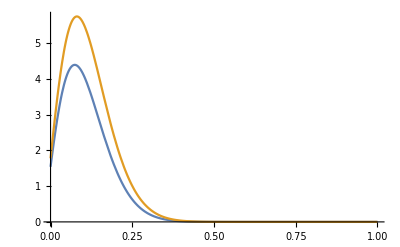

```mathematica
Plot[{Evaluate[haywardScenario3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

{{0.131545}}

```mathematica
Export["SimComparison_Scenario3_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario3_end",ToString[i],".csv"], {{val}},"csv"],
{i,0,1,0.01}]
```

0. xxxx 1.54287

0.01 xxxx 2.22725

0.02 xxxx 2.84745

0.03 xxxx 3.3766

0.04 xxxx 3.79866

0.05 xxxx 4.10685

0.06 xxxx 4.30195

0.07 xxxx 4.39046

0.08 xxxx 4.38297

0.09 xxxx 4.29264

0.1 xxxx 4.1339

0.11 xxxx 3.92146

0.12 xxxx 3.66948

0.13 xxxx 3.39107

0.14 xxxx 3.09783

0.15 xxxx 2.79972

0.16 xxxx 2.50495

0.17 xxxx 2.22003

0.18 xxxx 1.94987

0.19 xxxx 1.69794

0.2 xxxx 1.46643

0.21 xxxx 1.2565

0.22 xxxx 1.06842

0.23 xxxx 0.901785

0.24 xxxx 0.755666

0.25 xxxx 0.628782

0.26 xxxx 0.519613

0.27 xxxx 0.426506

0.28 xxxx 0.347763

0.29 xxxx 0.281705

0.3 xxxx 0.226722

0.31 xxxx 0.181303

0.32 xxxx 0.144062

0.33 xxxx 0.113748

0.34 xxxx 0.0892484

0.35 xxxx 0.0695859

0.36 xxxx 0.0539149

0.37 xxxx 0.0415107

0.38 xxxx 0.0317589

0.39 xxxx 0.0241444

0.4 xxxx 0.0182387

0.41 xxxx 0.0136892

0.42 xxxx 0.0102082

0.43 xxxx 0.00756269

0.44 xxxx 0.0055658

0.45 xxxx 0.00406882

0.46 xxxx 0.00295433

0.47 xxxx 0.00213038

0.48 xxxx 0.0015255

0.49 xxxx 0.0010846

0.5 xxxx 0.000765561

0.51 xxxx 0.000536384

0.52 xxxx 0.000372986

0.53 xxxx 0.000257369

0.54 xxxx 0.000176195

0.55 xxxx 0.000119652

0.56 xxxx 0.0000805828

0.57 xxxx 0.0000538109

0.58 xxxx 0.0000356204

0.59 xxxx 0.0000233679

0.6 xxxx 0.0000151884

0.61 xxxx 9.77799×10^-6

0.62 xxxx 6.233×10^-6

0.63 xxxx 3.93286×10^-6

0.64 xxxx 2.45541×10^-6

0.65 xxxx 1.51627×10^-6

0.66 xxxx 9.25724×10^-7

0.67 xxxx 5.58524×10^-7

0.68 xxxx 3.32846×10^-7

0.69 xxxx 1.95819×10^-7

0.7 xxxx 1.13665×10^-7

0.71 xxxx 6.5055×10^-8

0.72 xxxx 3.6688×10^-8

0.73 xxxx 2.03717×10^-8

0.74 xxxx 1.11285×10^-8

0.75 xxxx 5.9753×10^-9

0.76 xxxx 3.15039×10^-9

0.77 xxxx 1.62921×10^-9

0.78 xxxx 8.25405×10^-10

0.79 xxxx 4.09111×10^-10

0.8 xxxx 1.98065×10^-10

0.81 xxxx 9.34745×10^-11

0.82 xxxx 4.28911×10^-11

0.83 xxxx 1.90571×10^-11

0.84 xxxx 8.14932×10^-12

0.85 xxxx 3.31534×10^-12

0.86 xxxx 1.28893×10^-12

0.87 xxxx 5.06723×10^-13

0.88 xxxx 2.28886×10^-13

0.89 xxxx 1.52643×10^-13

0.9 xxxx 1.0414×10^-13

0.91 xxxx 6.53958×10^-15

0.92 xxxx -7.254×10^-14

0.93 xxxx -2.30737×10^-13

0.94 xxxx -2.25065×10^-13

0.95 xxxx -9.62474×10^-14

0.96 xxxx 8.60898×10^-14

0.97 xxxx 5.76541×10^-14

0.98 xxxx -2.77116×10^-13

0.99 xxxx -1.59266×10^-13

1. xxxx 3.35302×10^-12

```mathematica
(* Scenario 4*)
Clear[selCoef, genVar, blah, statDist];
selCoef = 0.01;
genVar = 0.056859878;
```

```mathematica
blah = NDSolve[{D[f[y,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[y(1-y)f[y,t],y] + 1/2 D[y(1-y)f[y,t],{y,2}],
f[y,0]==Evaluate[PDF[TriangularDistribution[{(start - 0.001),(start + 0.001)},start],y]]} /. {α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> genVar, W->fitVar},
f,{y,0,1},{t,0,0.25},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

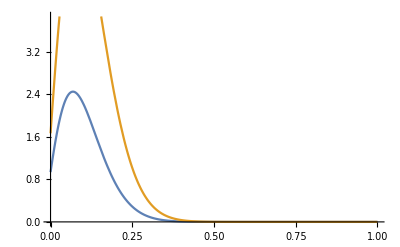

```mathematica
Plot[{Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}],
Evaluate[f[y,t] /.blah /. {t->time}]},{y, 0,1}]
```

```mathematica
statDist = 1/2 NIntegrate[Abs[Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar}] - Evaluate[{f[y, time]} /. blah]],{y,0,1}];
Print[statDist];
```

{{0.300916}}

```mathematica
Export["SimComparison_Scenario4_StatDist.csv", {{statDist}},"csv"];
```

```mathematica
Do[Clear[val];
val = Evaluate[haywardScenario4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->genVar,  W->fitVar, y -> i}];
Print[i," xxxx ", val];
Export[StringJoin["SimComparison_Scenario4_end",ToString[i],".csv"], {{val}},"csv"],
{i,0.36,1,0.01}]
```

$Aborted